Q^-1/ΔE 
d=1.5
with heat flow

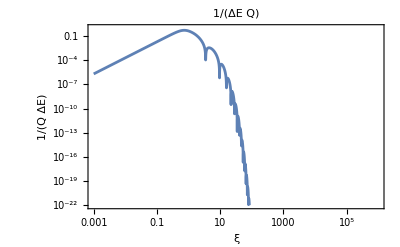

```mathematica
QHeatFlow15=Abs[3/(4 ξ^3)-1/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))]/.
{d->1.5};

QHeatFlowg=LogLogPlot[QHeatFlow15,{ξ,0.001,1000000},PlotLabel->Q^-1/ΔE, Frame->True,FrameLabel->{ξ,Q^-1/ΔE}]
```

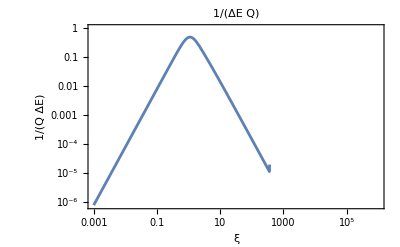

```mathematica
QHeatFlow1=Abs[3/(4 ξ^3)-1/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))]/.
{d->1};

QHeatFlow1g=LogLogPlot[QHeatFlow1,{ξ,0.001,1000000},PlotLabel->Q^-1/ΔE, Frame->True,FrameLabel->{ξ,Q^-1/ΔE}]
```

without heat flow

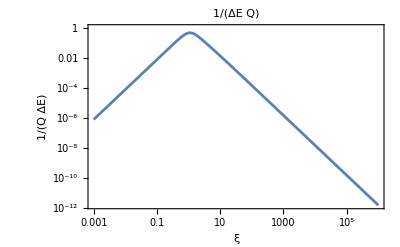

```mathematica
QNoHeatFlow =Abs[ 6/(2ξ)^2-6/(2ξ)^3(Sinh[2ξ]+Sin[2ξ])/(Cosh[2ξ]+Cos[2ξ]) ];

(*{ξ->b/2 √(ω/(2χ)),ξd->bd/2 √(ω/(2χ))}/.
{ω->2π f,χ->4.47,b->2 10^-3};*)
QNoHeatFlowg=LogLogPlot[QNoHeatFlow,{ξ,0.001,1000000},PlotLabel->Q^-1/ΔE, Frame->True,FrameLabel->{ξ,Q^-1/ΔE}]
```

並べる

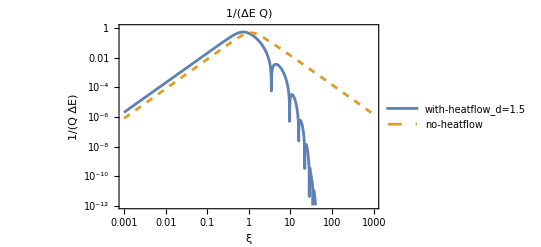

```mathematica
LogLogPlot[{QHeatFlow15,QNoHeatFlow},{ξ,0.001,1000},PlotStyle->{RightBlue,Dashed},PlotLegends->Placed[{"with-heatflow_d=1.5","no-heatflow"},{0.3,0.3}],PlotLabel->Q^-1/ΔE,Frame->True,FrameLabel->{ξ,Q^-1/ΔE}]
```

ディップ位置

```mathematica
FindArgMin[QHeatFlow15,{ξ,1,10}]
```

{3.47273}

```mathematica
FindArgMin[QHeatFlow15,{ξ,5,10}]
```

{9.53535}

```mathematica
FindArgMin[QHeatFlow15,{ξ,11,15}]
```

{15.7733}

```mathematica
FindArgMin[QHeatFlow15,{ξ,20,25}]
```

{22.0267}

```mathematica
FindArgMin[QHeatFlow15,{ξ,25,30}]
```

{28.1972}